The Order-Finding Algorithm |

Quantum Modular Exponentiationpaclet:Q3/tutorial/OrderFindingAlgorithm#115979312 | Quantum Implementationpaclet:Q3/tutorial/OrderFindingAlgorithm#1702961113

See also Section 4.5 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Let f be the modular exponentiation defined by

f(x)=a x   (mod  N)

for fixed positive integers a and N. The two integers a and N are assumed to be coprimes. The function is a periodic function,

a^r=1  (mod N)

for some integer r. The primary period (the smallest period) r is called the order of a modulo N. The order-fining problem is to determine the order for given a and N. It is known to be hard to solve classically.

The order-finding algorithm is the central part of the quantum factorization algorithm

PowerModpaclet:ref/PowerMod | Modular exponentiation
ContinuedFractionpaclet:ref/ContinuedFraction | Generates the continued fraction representation of a number
Convergentspaclet:ref/Convergents | Returns the convergents corresponding to a continued fraction

Functions used in the order-finding algorithm.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Quantum Modular Exponentiation

The order-finding problem is a specific case of the period-finding problem, where function f is not specified explicitly, but the corresponding quantum oracle is assumed to be implemented efficiently.

Unlike the period-finding algorithm, the order-finding algorithm does not resort to quantum oracle but conditional exponentiation. Or, putting it another way, the quantum oracle corresponding to the modular exponentiation is efficiently implemented by the conditional exponentiation,

x⊗y↦x⊗(U^x y) ,

of the quantum-adapted modular multiplication,

U:y↦a y (mod N) .

Note that repeated application of the modular multiplication gives the quantum adaptation of the modular exponentiation,

U^x y↦a^x y (mod N) .

Therefore, the order-finding algorithm is essentially the quantum phase estimation for the modular multiplication.

Quantum Implementation

Let us now formulate the order-finding problem more precisely in the form of quantum phase estimation.

Applying the modular multiplication r times should bring the system back to the original state. Therefore, the states

1, U1,U^2 1,…,U^(r-1)1

form a closed cycle. In physics, it is common to construct the eigenstates of U that generates the cycle with the discrete Fourier transform of the states in the list. By definition, the latter is the quantum Fourier transform. Indeed, define

ϕ_k:=1/(√r)∑_(x=0)^(r-1) U^x 1 ⅇ^(2π ⅈ x k/r)=1/(√r)∑_(x=0)^(r-1) a^x (mod N)ⅇ^(2π ⅈ x k/r)

for k=0,1,...,r−1. We see that

Uϕ_k:=1/(√r)∑_(x=0)^(r-1) a^(x+1) (mod N)ⅇ^(2π ⅈ x k/r)=ϕ_k ⅇ^(-2π ⅈ x k/r) .

In other words, ϕ_k is an eigenstate of U belonging to the eigenvalue ⅇ^(-2π ⅈ x k/r). Therefore, by preparing the target register in one of those eigenstates ϕ_k and applying the standard quantum phase estimation procedure, one would be able to estimate the “phase” 2π ϕ_k:=2π k/r. One would then find the order r from it.

Unfortunately, it is highly non-trivial to prepare an register in one of those eigenstates. Instead, we prepare the target register in a superposition of all eigenstates. This practice is in accordance with a common dictum in physics that a localized distribution in real space is unlocalized in the Fourier space and vice versa. Indeed, we find that

∑_(k=0)^(r-1) ϕ_k=1≡0⊗⋯⊗0⊗1 ,

which is straightforward to prepare. The cost is that the quantum phase estimation procedure randomly selects one from the possible values 0, 1/r, … , (r − 1)/r. Furthermore, the estimated phase ϕ is only approximate to one of the precise values ϕ_k=k/r. However, we have already seen how to overcome these difficulties in the period-finding algorithm, and the (classical) post-processing is exactly the same as in the period-finding algorithm.

There still remains a question when it comes to the performance of the order- finding algorithm. The performance of the algorithm relies on how efficiently one can perform the controlled- U^(2^k) gate (see Quantum Phase Estimation). As mentioned above, U^x is nothing but the quantum-adapted modular exponentiation. Fortunately, it is known that the modular exponentiation can be implemented efficiently on a quantum computer (Vedral et al., 1996).

Let V be the modular multiplication on two registers (to be compared with U with fixed a,

V:x⊗y↦x⊗x y (mod N) .

The basic idea is to duplicate the logical state, x⊗0 ↦x⊗x by employing the CNOT gate, and then to apply the modular multiplication on the two registers, x⊗x ↦x⊗x^2(mod N). Repeating the procedure k times produces the desired result. For example, the following quantum circuit effectively performs U^(2^3),

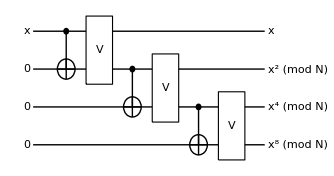

where each horizontal line denotes a register of n qubits, not a single qubit, and x=0,1,…, 2^n−1.

| Related Guides
▪Quantum Computation and Quantum Information

| Related Tutorials
▪Abelian Hidden Subgroup Problems
▪Quantum Algorithms
▪Quantum Computation and Quantum Information with Q3

| Related Links
▪V. Vedral, A. Barenco, and A. Ekert, Physical Review A 54 (1), 147 (1996)https://doi.org/10.1103/physreva.54.147, “Quan- tum networks for elementary arithmetic operations.”
▪M. Nielsen and I. L. Chuang, Quantum Computation and Quantum Information (Cambridge University Press, New York, 2011)https://doi.org/10.1017/CBO9780511976667.
▪Mahn-Soo Choi, A Quantum Computation Workbook (Springer, 2021)https://doi.org/10.1007/978-3-030-91214-7.